# 第3章 微积分

## 3.1 求极限

计算函数极限的形式：Limit [ expr, x -> x0]

例1 ： 求下列极限
(1) lim_(x→0) sin(a x)/x       (2)lim_(x→1) (m/(1-x^m)-n/(1-x^n))

```mathematica
Clear["Global`*"]
Limit[Sin[a x]/x, x -> 0]
```

a

```mathematica
Limit[m/(1-x^m)-n/(1-x^n), x->1]
```

(m-n)/2

不是所有的函数都有确定的极限，例如 , 极限不存在，在0附近，函数在[-1, 1] 之间波动，Limit运算的结果是一个区间。

```mathematica
Limit[Sin[1/x],x->0]
(1+%)^2*5
```

Indeterminate

Indeterminate

数列的极限，可以用同样的形式进行计算。

```mathematica
Limit[Sqrt[n + Sqrt[n]]- Sqrt[n], n -> Infinity]
```

1/2

```mathematica
Limit[n!/n^n, n -> Infinity]
```

0

有些函数在特定点处，从不同方向趋于该点有不同极限,使用 limit 中的 Direction 选项， 可以指定趋近的方向.
Limit[expr, x -> x0] | 计算 x → x0时函数expr 的极限
Limit[expr, x -> x0, Direction -> 1] | 计算x → x0时函数expr的左极限
Limit[expr, x -> x0, Direction -> -1] | 计算x → x0时函数expr的右极限

```mathematica
Limit[Log[x]/x, x -> 0, Direction -> -1]
```

-∞

```mathematica
Limit[ArcTan[1/x], x->0, Direction->1]
```

-π/2

```mathematica
Limit[Gamma[x + 1/2]/(Sqrt[x]*Gamma[x]),  x -> Infinity]
```

1

Limit 函数自己不带对多个变量取极限的功能即不能计算重极限，可以计算累次极限。

```mathematica
Limit[Limit[((x*y)/(x^2 + y^2))^(x^2),  x -> Infinity],y -> Infinity]
```

0

```mathematica
Limit[Limit[((x*y)/(x^2 + y^2))^(x^2),  y -> Infinity], x -> Infinity]
```

0

还可以计算自变量沿某一固定路径趋向于固定点时，表达式的极限

```mathematica
Clear[t,a,x,y]
```

```mathematica
Limit[(x^2+y^2)/(1-(1+x^2+y^2)^(1/2))/.{y->a t^2,x->t},t->0]
```

-2

## 3.2 微商和微分

### 1.偏微分

D[f,x] | 偏导数(∂f/∂x)
D[f,x1,x2,.85,xn] | 高阶偏导数
D[f,{x,n}] | n阶导数
D[f,x,NonConstants→{y1,y2,...,ym}] | 复合函数的偏导数∂f/∂x，y1,...,ym是x的函数
D[f,{{x,y,z,...}}] | 偏导向量(∂f/∂x,∂f/∂y,∂f/∂z,...)
   对于一元函数来说，指令D求的是变量的导数，对于多元函数，求的是偏导数，假定其余变量均与要求导的变量无关，若求复合函数的偏导，需给出假设条件NonConstants→{z}，指明变量z 是依赖其他变量的函数.

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^n,{x,2}]
```

(-1+n) n x^(-2+n)

```mathematica
D[z (x^2+y^2),x,y]
```

0

```mathematica
D[z (x^2+y^2),{x,2}]
```

2 z

```mathematica
D[z (x^2+y^2),{{x,y}}]
```

{2 x z,2 y z}

```mathematica
D[z (x^2+y^2),{{x,y,z},2}]
```

{{2 z,0,2 x},{0,2 z,2 y},{2 x,2 y,0}}

```mathematica
{{2 z,0,2 x},{0,2 z,2 y},{2 x,2 y,0}}//MatrixForm
```

(2 z | 0 | 2 x
0 | 2 z | 2 y
2 x | 2 y | 0)

```mathematica
D[z (x^2+y^2),{{x,y}},NonConstants->{z}]
```

{2 x z+(x^2+y^2) D[z,x,NonConstants→{z}],2 y z+(x^2+y^2) D[z,y,NonConstants→{z}]}

### 2. 全微分与全导数

Dt[f] | f的全微分
Dt[f,x] | f的全导数
Dt[f,{x,n}] | f对x的n阶导数
Dt[f,x1,x2,…] | f的混合导数
Dt[f,x,Constants→{c1,c2,…}] | "全导数,c1,c2,…不依赖于x"

```mathematica
D[x^2+y^2,x]
```

2 x

```mathematica
Dt[x^2+y^2,x]
```

2 x+2 y Dt[y,x]

```mathematica
Dt[x^2+y^2,x,Constants->{y}]
```

2 x

```mathematica
Dt[x^2+y^2]
```

2 x Dt[x]+2 y Dt[y]

```mathematica
Dt[x^2+y^2+z^2,{x,2}]
```

2+2 Dt[y,x]^2+2 y Dt[y,{x,2}]+2 Dt[z,x]^2+2 z Dt[z,{x,2}]

### 3.抽象函数的导数表示

"f'[x]" | "单变量函数的导数"
"f^(n)[x]" | "单变量函数的n阶导数"
"f^(n1,n2,...)[x1,x2,...]" | "多变量函数的混合偏导"

```mathematica
(Log[x]*Sin[x])'
```

(Log[x] Sin[x])'

```mathematica
f[x_]:=Sin[x];
{f'[x],f''[x],f'''[x],(f^(4))[x]}
```

{Cos[x],-Sin[x],-Cos[x],f^4[x]}

```mathematica
Clear[f]
```

```mathematica
D[f[x],{x,4}]
```

f^(4)[x]

```mathematica
Clear[h]
```

```mathematica
D[h[x,y],{x,3},{y,2}]
```

h^(3,2)[x,y]

用户可以定义单变量函数 f 在 Mathematica 中的导数,这只需简单地进行赋值即可.
例如 定义f'[x_] := h f[x] + g f[x].接下来就可以根据定义的规则计算导数.

```mathematica
Clear[f,g]
```

```mathematica
f'[x_] := h f[x] + g f[x]
D[f[x^2],x]
f'[x^2]
```

2 x (g f[x^2]+h f[x^2])

g f[x^2]+h f[x^2]

例：对于函数, 求出使得微分中值定理在区间[0, 2] 上成立的值.

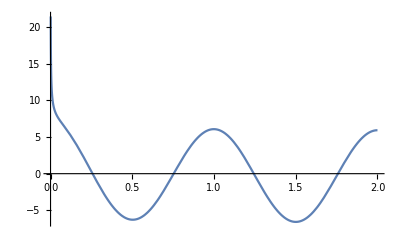

```mathematica
Clear[f,a,b];
f[x_]:=Sqrt[x]+Sin[2π x];
a=0;b=2;m=(f[b]-f[a])/b-a;
Plot[f'[x]-m,{x,0,2}]
```

```mathematica
t1=FindRoot[f'[x]==m,{x,0.3}]
t2=FindRoot[f'[x]==m,{x,0.7}]
t3=FindRoot[f'[x]==m,{x,1.3}]
t4=FindRoot[f'[x]==m,{x,1.7}]
```

{x→0.257071}

{x→0.753319}

{x→1.24344}

{x→1.75836}

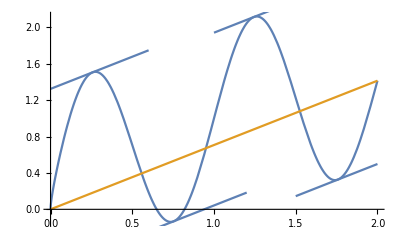

```mathematica
g=Plot[{f[x],m x},{x,0,2}];
g1=Plot[m(x-0.25707061913)+f[0.25707061913],{x,0,0.6}];
g2=Plot[m(x-0.753319266)+f[0.753319266],{x,0.5,1.2}];
g3=Plot[m(x-1.243444795)+f[1.243444795],{x,1.0,1.6}];
g4=Plot[m(x-1.75836391)+f[1.75836391],{x,1.5,2.0}];
Show[{g,g1,g2,g3,g4}]
```

### 4.导数应用

■FindMinimum[f[x], x]                                     从自动选择的点计算极小值及点坐标
■FindMinimum[f[x], {x, x0}]                          求出f (x) 靠近x0点的极小值点和极小值
■FindMinimum[f, {{x, x0}, {y, y0}, …}]       多变量函数在指定点附近的极小值

FindMinimum利用修正的最速下降法计算函数的极小值, 可以用选项 Method -> Newton, Method -> QuasiNewton改变所用的方法.
求极大值可以用 FindMaximum[f[x], {x, x0}] 等.

例题：求f(x)=x+Sin(3x)在[0,Pi]中的极小值和极大值.

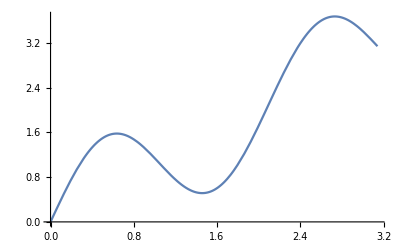

```mathematica
f[x_]:=x+Sin[3x];
Plot[x+Sin[3x],{x,0,Pi}]
```

```mathematica
FindMinimum[f[x],{x,1.0}]
```

{0.514708,{x→1.45752}}

```mathematica
{FindMaximum[f[x],{x,0.5}],FindMaximum[f[x],{x,2.5}]}
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{1.57969,{x→0.636878}},{3.67408,{x→2.73127}}}

例：求函数f (x, y, z) = x y z满足x^2 + 2 y^2 + 3 z^2 = 6 条件下的条件极值.

```mathematica
Clear[f,g,cond,x,y,z,a];
f[x_,y_,z_]=x y z;
g[x_,y_,z_]=x^2+2y^2+3z^2-6;
cond=Eliminate[{D[f[x,y,z],x]==a D[g[x,y,z],x],D[f[x,y,z],y]==a D[g[x,y,z],y],D[f[x,y,z],z]==a D[g[x,y,z],z],g[x,y,z]==0},a]
```

x^2==6-2 y^2-3 z^2&&4 y^2 z==z (6-3 z^2)&&x (2 y^2-3 z^2)==0&&x y (-2+3 z^2)==0&&x z (-2+3 z^2)==0&&y z (-2+3 z^2)==0&&4 z-8 z^3+3 z^5==0&&y^3+y (-3+3 z^2)==0

```mathematica
points=Solve[cond, {x,y,z}]
```

{{x→-√6,y→0,z→0},{x→√6,y→0,z→0},{x→0,y→-√3,z→0},{x→0,y→√3,z→0},{x→-√2,y→-1,z→-√(2/3)},{x→√2,y→-1,z→-√(2/3)},{x→-√2,y→1,z→-√(2/3)},{x→√2,y→1,z→-√(2/3)},{x→-√2,y→-1,z→√(2/3)},{x→√2,y→-1,z→√(2/3)},{x→-√2,y→1,z→√(2/3)},{x→√2,y→1,z→√(2/3)},{x→0,y→0,z→-√2},{x→0,y→0,z→√2}}

```mathematica
value=f[x,y,z]/.points
```

{0,0,0,0,-2/(√3),2/(√3),2/(√3),-2/(√3),2/(√3),-2/(√3),-2/(√3),2/(√3),0,0}

```mathematica
Min[value]
Max[value]
```

-2/(√3)

2/(√3)

#### 3. 矢量运算

■Div[{f1, f2, f3}, {var}, .94coordsys.94]                                     按设定的坐标系计算散度
■Div[{f1, f2, f3}, {x, y, z}]                                                     按直角坐标系计算散度
■Curl[{f1, f2, f3}, {x1, x2, x3}, .94coordsys.94]                       按设定的坐标系计算旋度
■Curl[{f1, f2, f3}, {x1, x2, x3}]                                           按直角坐标系计算旋度
■Grad[f, {x, y, z}]                                                                   按直角坐标系计算梯度
■Laplacian[f, {x, y, z}]                                                        计算Δf (x, y, z)

```mathematica
Clear[F,f,x,y,z]
F={Sqrt[x^2+y^2+z^2],2x y,Sin[z]/(x+y)};
```

```mathematica
Div[F,{x,y,z}]
Curl[F,{x,y,z}]
```

2 x+x/(√(x^2+y^2+z^2))+Cos[z]/(x+y)

{-Sin[z]/(x+y)^2,z/(√(x^2+y^2+z^2))+Sin[z]/(x+y)^2,2 y-y/(√(x^2+y^2+z^2))}

```mathematica
Grad[Sqrt[x^2+y^2+z^2],{x,y,z}]
Laplacian[f[x,y,z],{x,y,z}]
```

{x/(√(x^2+y^2+z^2)),y/(√(x^2+y^2+z^2)),z/(√(x^2+y^2+z^2))}

f^(0,0,2)[x,y,z]+f^(0,2,0)[x,y,z]+f^(2,0,0)[x,y,z]

■设定坐标系："Polar"，"Cylindrical"，"Spherical"

```mathematica
Curl[{f[r,θ,z],g[r,θ,z],h[r,θ,z]},{r,θ,z},"Cylindrical"]
Grad[r^2 Sin[theta],{r,theta,phi}]
```

{-6 z+(h^(0,1,0)[r,θ,z])/r,f^(0,0,1)[r,θ,z]-h^(1,0,0)[r,θ,z],2 r-(6-r^2-3 z^2-2 θ^2+f^(0,1,0)[r,θ,z])/r}

{2 r Sin[theta],r^2 Cos[theta],0}

## 3.3 不定积分和定积分

### 1. 不定积分

■￿Integrate[f, x] 计算不定积分，输出结果中省略积分常数。
■￿Integrate[f, x, y] 计算二重积分，积分的顺序是从右自左，先对变量y做积分计算，再对变量x做积分计算
Integreate主要计算只含有 "简单函数" 的被积函数。"简单函数" 包括有理函数、指数函数、对数函数、三角和反三角函数。

```mathematica
Integrate[3 a x^2,x]
```

a x^3

```mathematica
Integrate[Sqrt[x^2-a^2],x]
```

1/2 x √(-a^2+x^2)-1/2 a^2 Log[x+√(-a^2+x^2)]

```mathematica
Integrate[Sqrt[Cos[x]],x]
```

2 EllipticE[x/2,2]

```mathematica
Integrate[1/(1+x^4),x]
```

(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 √2)

```mathematica
TraditionalForm[%]
```

(-log(x^2-√2 x+1)+log(x^2+√2 x+1)-2 tan^-1(1-√2 x)+2 tan^-1(√2 x+1))/(4 √2)

Mathematica 可以计算在标准积分表中能找到的初等函数的反导数，但是如果不能用初等函数表示反导数，这个软件就会尝试用特殊函数表示反导数.如果这还不行的话, 它就会返回无法计算的积分

```mathematica
Integrate[Sin[x^2],x]
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
Integrate[Sin[Sin[x]],x]
```

∫Sin[Sin[x]]ⅆx

Integrate可以计算形式上的积分

```mathematica
Integrate[E^x*(f[x]+f'[x]),x]
```

ⅇ^x f[x]

Integrate可以计算分段函数积分

```mathematica
Integrate[Piecewise[{{1,x<1},{x,x⩾1}}],x]
```

Piecewise[{{x, x≤1}, {1/2+x^2/2, True}}]

Mathematica可以对向量值函数积分

```mathematica
Integrate[{x,E^x,Sin[x]},x]
```

{x^2/2,ⅇ^x,-Cos[x]}

### 2. 定积分

■Integrate[f, {x, a, b}]                                      计算定积分的准确解
■NIntegrate[f, {x, a, b}]                                  计算定积分的数值解
■Integrate[f, {x, a, b}, {y, c, d}]                    计算定积分的准确解
■NIntegrate[f, {x, a, b}, {y, c, d}]                计算定积分的数值解

对简单情形，求定积分可通过先求不定积分然后计算相应积分限处的值.但许多函数的不定积分不能用标准数学函数表出.但其定积分仍然能求出.

```mathematica
Integrate[Cos[Sin[x]],x]
```

∫Cos[Sin[x]]ⅆx

```mathematica
Integrate[Cos[Sin[x]],{x,0,Pi}]
```

π BesselJ[0,1]

广义积分Cauchy主值 Integrate[f, {x, xmin, xmax}, PrincipalValue -> True]

```mathematica
Integrate[1/x, {x, -1, 2}, PrincipalValue->True]
```

Log[2]

计算二重积分，要注意积分顺序

```mathematica
Integrate[x+y,{x,1,2},{y,1,x}]
Integrate[x+y,{y,1,x},{x,1,2}]
```

3/2

-1/2+3/2 (-1+x)+x^2/2

例：计算二重积分∫∫_D ⅇ^(-(x^2+y^2))ⅆxⅆy，其中D为单位圆内部

解：用极坐标计算

```mathematica
f[x_,y_]:=Exp[-x^2-y^2];
a=1;
Integrate[r f[r Cos[t],r Sin[t]],{r,0,2 Pi},{r,0,a}]
```

((-1+ⅇ) π)/ⅇ

例：计算二重积分(∫∫_D ArcTan[y/x]ⅆxⅆy)，其中D={(x,y)|1≤x^2+y^2≤4,  0≤y≤x}

```mathematica
f[x_,y_]:=ArcTan[y/x];
Integrate[r f[x,y]/.{x->r Cos[t],y->r Sin[t]},{t,0,Pi/4},{r,1,2}]
```

(3 π^2)/64

例：利用二重积分汁算由抛物线 y = x^2 - 2 x + 2 与直线y = x + 1 围成区域的面积.

```mathematica
intersection=Solve[x^2-2x+2==x+1,x]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

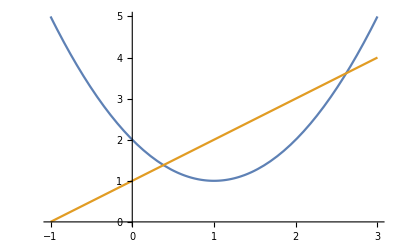

```mathematica
Plot[{x^2-2x+2,x+1},{x,-1,3}]
```

```mathematica
a=intersection[[1,1,2]];
b=intersection[[2,1,2]];
Integrate[1,{x,a,b},{y,x^2-2x+2,x+1}]
```

1/2 (-3-√5)+1/2 (3-√5)+1/24 (3-√5)^3-1/24 (3+√5)^3+3 (-1/8 (3-√5)^2+1/8 (3+√5)^2)

解法2：用Boole函数定义积分区域

```mathematica
Integrate[Boole[(y≥x^2-2x+2)&&(y≤x+1)],{x,0,3},{y,0,5}]
```

(5 √5)/6

利用定积分的计算公式，我们可以计算三重积分，曲线积分，曲面积分等，下面看几个例子.

例：计算∫∫∫_V xy^2 z^3 ⅆxⅆyⅆz 其中V是由曲面z=xy,z=0,y=x,x=1围成。

```mathematica
Clear[x,y,z]
Integrate[x*(y^2)*(z^3),{x,0,1},{y,0,x},{z,0,(x*y)}]
```

1/364

例 计算三重积分∫∫∫_v zⅆxⅆyⅆz，其中V:x^2+y^2≤z≤4

先用直角坐标

```mathematica
f[x_,y_,z_]:=z;
Integrate[f[x,y,z],{x,-2,2},{y,-Sqrt[4-x^2],Sqrt[4-x^2]},{z,x^2+y^2,4}]
```

(64 π)/3

再用柱面坐标计算

```mathematica
Integrate[r f[x,y,z]/.{x->r Cos[t],y->r Sin[t]},{t,0,2Pi},{r,0,2},{z,r^2,4}]
```

(64 π)/3

例 (球面坐标) 计算三重积分(∫∫∫_V √(x^2+y^2+z^2)ⅆxⅆyⅆz)，其中 V:x^2+y^2+z^2<z

```mathematica
f[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
Integrate[r^2 Sin[phi] f[x,y,z]/.{x->r Sin[phi] Cos[t],y->r Sin[phi]Sin[t],z->r Cos[phi]},{t,0,2Pi},{phi,0,Pi/2},{r,0,Cos[phi]}]
```

π/10

例 (参数曲线) 计算曲线积分∫_L x^2+y^2 ⅆs，其中 L:x=a(cos{t}+tsin{t}), y=a(sin{t}-tcos{t})（0<t<2Pi）

```mathematica
f[x_,y_]:=x^2+y^2;
x[t_]:=a (Cos[t]+t Sin[t]);y[t_]:=a (Sin[t]-t Cos[t]);
Integrate[Sqrt[x'[t]^2+y'[t]^2]*f[x,y]/.{x->x[t],y->y[t]},{t,0,2Pi}]
```

(18-8 √5) (π^2+2 π^4)

例:计算曲线积分 ∫_L x^2 ⅆx+zⅆy-yⅆz，其中L: x=kt, y=acost, z=asint, (0≤t≤π)

```mathematica
P[x_,y_,z_]:=x^2;Q[x_,y_,z_]:=z;R[x_,y_,z_]:=-y;
x[t_]:=k t;y[t_]:=a Cos[t];z[t_]:=a Sin[t];
Integrate[(x'[t]P[x,y,z]/.{x->x[t],y->y[t],z->z[t]})+(y'[t]Q[x,y,z]/.{x->x[t],y->y[t],z->z[t]})+(z'[t]R[x,y,z]/.{x->x[t],y->y[t],z->z[t]}),{t,0,Pi}]
```

-(7 π)/2+(3 √5 π)/2+(k^3 π^3)/3

例 求曲面  z=x^2+2y 在区域D: {(x,y)|0≤x≤1, 0≤y≤x}上那部分的面积.

```mathematica
f[x_,y_]:=x^2+2 y;
A=Sqrt[1+D[f[x,y],x]^2+D[f[x,y],y]^2]
Integrate[A,{x,0,1},{y,0,x}]
```

√(5+4 x^2)

9/4-(5 √5)/12

例 计算曲面积分 ∫∫_Σ (x^2+y^2)zⅆS，Σ:x^2+y^2+z^2=4, z≥0

解1.用直角坐标方程计算 （）

```mathematica
Clear[x,y,F,f,z]
```

```mathematica
f[x_,y_,z_]:=(x^2+y^2)z;
F[x_,y_]:=Sqrt[4-x^2-y^2];
A=Sqrt[1+D[F[x,y],x]^2+D[F[x,y],y]^2];
B=A f[x,y,z]/.{z->F[x,y]};
Integrate[r B/.{x->r Cos[t],y->r Sin[t]},{t,0,2Pi},{r,0,2}]
```

16 π

```mathematica
f[x_,y_,z_]:=(x^2+y^2) z;
x[t_,phi_]:=2Sin[phi]Cos[t];y[t_,phi_]:=2Sin[phi]Sin[t];z[t_,phi_]:=2Cos[phi];
r[t_,phi_]:={x[t,phi],y[t,phi],z[t,phi]}
A=Norm[Cross[D[r[t,phi],t],D[r[t,phi],phi]]];
B=(f[x,y,z]/.{x->x[t,phi],y->y[t,phi],z->z[t,phi]}) A;
Integrate[B,{t,0,2 Pi},{phi,0,Pi/2}]
```

16 π

例 计算曲面积分∫∫_Σ zdydz+ydzdx+xdxdy，Σ:x^2+y^2+z^2=1（外侧）

```mathematica
P[x_,y_,z_]:=z;Q[x_,y_,z_]:=y;R[x_,y_,z_]:=x;
F={P[x,y,z],Q[x,y,z],R[x,y,z]};
x[t_,phi_]:=Sin[phi]Cos[t];y[t_,phi_]:=Sin[phi]Sin[t];z[t_,phi_]:=Cos[phi];
r[t_,phi_]:={x[t,phi],y[t,phi],z[t,phi]};
A=Cross[D[r[t,phi],phi],D[r[t,phi],t]];
F=F/.{x->x[t,phi],y->y[t,phi],z->z[t,phi]};
Integrate[F.A,{t,0,2Pi},{phi,0,Pi}]
```

(4 π)/3

## 3.4 幂级数

### 1. 幂级数的展开

■Series[expr, {x, x0, n}] 将expr在x = x0点展开到n阶的幂级数
■Series[expr, {x, x0, n}, {y, y0, m}] 先对y展开到 m阶再对x展开n阶幂级数

```mathematica
Series[Sin[x^2],{x,0,15}]
```

x^2-x^6/6+x^10/120-x^14/5040+O[x]^16

```mathematica
Clear[f,a]
Series[f[x],{x,a,3}]
```

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+1/6 f^(3)[a] (x-a)^3+O[x-a]^4

```mathematica
Series[Sin[x]*Cos[y],{x,0,5},{y,0,5}]
```

(1-y^2/2+y^4/24+O[y]^6) x+(-1/6+y^2/12-y^4/144+O[y]^6) x^3+(1/120-y^2/240+y^4/2880+O[y]^6) x^5+O[x]^6

（1） Series 可以生成多个变量的幂级数, Series 对变量的运算顺序与 Integrate, Sum 等是一样的，首先展开的是最后一个指定的变量.（2） 展开式中可能将分数指数，对数函数等作为基本元素

```mathematica
Series[Sqrt[x],{x,0,10}]
```

√x+O[x]^(21/2)

```mathematica
Series[Sqrt[1+x],{x,0,10}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256-(21 x^6)/1024+(33 x^7)/2048-(429 x^8)/32768+(715 x^9)/65536-(2431 x^10)/262144+O[x]^11

```mathematica
Series[Exp[Sqrt[x]],{x,1,6}]
```

ⅇ+1/2 ⅇ (x-1)+1/48 ⅇ (x-1)^3-5/384 ⅇ (x-1)^4+3/320 ⅇ (x-1)^5-(329 ⅇ (x-1)^6)/46080+O[x-1]^7

```mathematica
Series[x^x,{x,0,4}]
```

1+Log[x] x+1/2 Log[x]^2 x^2+1/6 Log[x]^3 x^3+1/24 Log[x]^4 x^4+O[x]^5

（3） Series命令可以计算无界函数在瑕点的洛朗展开式, 展开式的最高次数可以是负数。

```mathematica
Series[1/((E^x-1)^10),{x,0,-2}]
```

1/x^10-5/x^9+145/(12 x^8)-75/(4 x^7)+3013/(144 x^6)-285/(16 x^5)+4523/(378 x^4)-6515/(1008 x^3)+7129/(2520 x^2)+1/O[x]

```mathematica
Series[Exp[1/x],{x,Infinity,6}] (*x=0是本性奇点*)
```

1+1/x+1/(2 x^2)+1/(6 x^3)+1/(24 x^4)+1/(120 x^5)+1/(720 x^6)+O[1/x]^7

### 2. 幂级数的运算

#### （1） 幂级数的简单运算

```mathematica
t=Series[Exp[x],{x,0,4}]
t^2
D[t,x]
Integrate[%,x]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

1+2 x+2 x^2+(4 x^3)/3+(2 x^4)/3+O[x]^5

1+x+x^2/2+x^3/6+O[x]^4

x+x^2/2+x^3/6+x^4/24+O[x]^5

例：求幂级数 ∑_(n=0)^∞ x^(4n+1)/(4n+1)的收敛域及和函数。

```mathematica
a[n_]:=1/(4*n+1);
f[x_,n_]:=a[n]*x^(4 n+1);
r=Limit[Abs[a[n+1]/a[n]],n->Infinity]
```

1

检查端点是否收敛

```mathematica
Sum[f[1,n],{n,1,Infinity}]
Sum[f[-1,n],{n,1,Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/(1+4 n)

Sum::div: Sum does not converge.

∑_(n=1)^∞ (-1)^(1+4 n)/(1+4 n)

两个端点都是发散点。收敛域 （-1, 1）

```mathematica
Sum[f[x,n],{n,1,Infinity}]
Sum[D[f[x,n],x],{n,1,Infinity}]
Integrate[%,x]
```

x (-1+Hypergeometric2F1[1/4,1,5/4,x^4])

-x^4/(-1+x^4)

-x+ArcTan[x]/2-1/4 Log[1-x]+1/4 Log[1+x]

#### （2） 给出幂级数中某一项的系数

■SeriesCoefficient[f, n] 级数f中x^n的系数
■SeriesCoefficient[f, {x, x0, n}] 函数f在x0的展开式中 (x - x0)^n的系数

```mathematica
SeriesCoefficient[Sin[x],{x,0,3}]
SeriesCoefficient[Exp[x],{x,0,n}]
```

-1/6

Piecewise[{{1/(n!), n≥0}, {0, True}}]

#### (3)幂级数的复合与反演

■ComposeSeries[sreies1, series2, .85]，复合幂级数
■InverseSeries[series，x]                         反演幂级数

```mathematica
a=Series[Exp[x],{x,0,11}];
b=Series[Sin[x],{x,0,11}];
ComposeSeries[a,b]
Series[Exp[Sin[x]],{x,0,11}]
```

1+x+x^2/2-x^4/8-x^5/15-x^6/240+x^7/90+(31 x^8)/5760+x^9/5670-(2951 x^10)/3628800-x^11/3150+O[x]^12

1+x+x^2/2-x^4/8-x^5/15-x^6/240+x^7/90+(31 x^8)/5760+x^9/5670-(2951 x^10)/3628800-x^11/3150+O[x]^12

用函数y = f (x) 的幂级数，计算反函数x = f^(-1) (y) 的幂级数，求出的结果用x做自变量表示。

```mathematica
s=Series[Sin[x],{x,0,7}]
InverseSeries[s]
Series[ArcSin[x],{x,0,7}]
InverseSeries[s,y] (*x=Sin^(-1)[y]的幂级数，自变量为y*)
```

x-x^3/6+x^5/120-x^7/5040+O[x]^8

x+x^3/6+(3 x^5)/40+(5 x^7)/112+O[x]^8

x+x^3/6+(3 x^5)/40+(5 x^7)/112+O[x]^8

y+y^3/6+(3 y^5)/40+(5 y^7)/112+O[y]^8

■Normal[series] 表达式 将幂级数转为正常的表达式截断幂级数，假定高阶项为0

```mathematica
Normal[s]
Factor[%]
```

x-x^3/6+x^5/120-x^7/5040

-(x (-5040+840 x^2-42 x^4+x^6))/5040

### 3. Fourier级数

■FourierSeries[expr, t, n] 给出关于 t 的expr 的n阶傅里叶级数展开式
■FourierSeries[expr, {t1, t2, .85}, {n1, n2, .85}] 给出一个多维傅里叶级数

```mathematica
a=FourierSeries[t^2,t,4]
ExpToTrig[a]
b=FourierSeries[t^2,t,6]
c=FourierSeries[t^2,t,8]
```

FourierSeries[1+2 x+2 x^2+(4 x^3)/3+(2 x^4)/3+O[x]^5,1+x+x^2/2+x^3/6+x^4/24+O[x]^5,4]

FourierSeries[1+2 x+2 x^2+(4 x^3)/3+(2 x^4)/3+O[x]^5,1+x+x^2/2+x^3/6+x^4/24+O[x]^5,4]

FourierSeries[1+2 x+2 x^2+(4 x^3)/3+(2 x^4)/3+O[x]^5,1+x+x^2/2+x^3/6+x^4/24+O[x]^5,6]

FourierSeries[1+2 x+2 x^2+(4 x^3)/3+(2 x^4)/3+O[x]^5,1+x+x^2/2+x^3/6+x^4/24+O[x]^5,8]

```mathematica
FourierSeries[x^2 y,{x,y},{2,2}]
```

-1/4 ⅈ ⅇ^(ⅈ (-2 x-2 y))+ⅈ ⅇ^(ⅈ (-x-2 y))+ⅈ ⅇ^(ⅈ (x-2 y))-1/4 ⅈ ⅇ^(ⅈ (2 x-2 y))+1/2 ⅈ ⅇ^(ⅈ (-2 x-y))-2 ⅈ ⅇ^(ⅈ (-x-y))-2 ⅈ ⅇ^(ⅈ (x-y))+1/2 ⅈ ⅇ^(ⅈ (2 x-y))-1/2 ⅈ ⅇ^(ⅈ (-2 x+y))+2 ⅈ ⅇ^(ⅈ (-x+y))+2 ⅈ ⅇ^(ⅈ (x+y))-1/2 ⅈ ⅇ^(ⅈ (2 x+y))+1/4 ⅈ ⅇ^(ⅈ (-2 x+2 y))-ⅈ ⅇ^(ⅈ (-x+2 y))-ⅈ ⅇ^(ⅈ (x+2 y))+1/4 ⅈ ⅇ^(ⅈ (2 x+2 y))+1/3 ⅈ ⅇ^(-ⅈ y) π^2-1/3 ⅈ ⅇ^(ⅈ y) π^2-1/6 ⅈ ⅇ^(-2 ⅈ y) π^2+1/6 ⅈ ⅇ^(2 ⅈ y) π^2

## 3.5 微分方程

### 1.常微分方程

求解常微分方程和常微分方程组的一般形式：
■DSolve [eqns, y[x], x]	                                      解y(x)的微分方程或方程组 eqns，x为变量。
■DSolve [eqns, y, x]	                                      在纯函数的形式下求解，纯函数部分请看第7章。

DSolve 返回的结果是一个函数规则列表.问题是这些函数如何被表示.如果要求
DSolve 关于 y[x] 求解，那么 Solve 将返回 y[x] 的规则.如果用户需要符号形式的解，那么引入哑变量可能是方便的.但是，如果打算将解用于各种其它运算中，那么最好是得到不带哑变量的纯函数形式的解.

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x]
y[x]+2y'[x]+y[0]/.%
```

{{y[x]→1+ⅇ^-x C[1]}}

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
DSolve[y'[x]+y[x]==1,y,x]
y[x]+2y'[x]+y[0]/.%
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

{2+C[1]-ⅇ^-x C[1]}

一阶微分方程的通解中一般有一个任意常数，用c1表示，可以通过给定初始条件确定参数的值，一般 n阶方程有n个参数，用c1, c2.85表示.

```mathematica
DSolve[y''''[x]==y[x],y[x],x]
DSolve[{y''''[x]==y[x],y[0]==y'[0]==1},y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]}}

{{y[x]→ⅇ^-x (1-C[1]+ⅇ^(2 x) C[1]-C[2]+ⅇ^x C[2] Cos[x]+2 ⅇ^x Sin[x]-2 ⅇ^x C[1] Sin[x]-ⅇ^x C[2] Sin[x])}}

求微分方程解的精确公式是困难的事情.事实上，只有很少种类的方程能求出这样的
公式解.包含高阶导数的方程，就不一定能求出解.一些简单的二阶线性方程的解被当做特殊函数来表示其它方程的解。

```mathematica
DSolve[y''[x]+y'[x]+y[x]^2==0,y[x],x]         (*无法求解*)
```

DSolve[y[x]^2+y'[x]+y''[x]==0,y[x],x]

```mathematica
DSolve[x^2  y''[x] + x  y'[x] + x^2 y[x] == 0, y[x], x](*Bessel方程*)
```

{{y[x]→BesselJ[0,x] C[1]+BesselY[0,x] C[2]}}

```mathematica
DSolve[y'[x] == x*y[x] + 1, y[x], x]
```

{{y[x]→ⅇ^(x^2/2) C[1]+ⅇ^(x^2/2) √(π/2) Erf[x/(√2)]}}

微分方程组也用同一个指令求解。

```mathematica
DSolve[{y[x] == -z'[x], z[x] == -y'[x]}, {y, z}, x]
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

### 2. 偏微分方程

■DSolve[{eqn1, eqn2, ...}, y[x1, x2, ... .85], {x1, x2, ...}]                            计算偏微分方程组的准确解
■DSolve[eqn, y[x1, x2, ...], {x1, x2, ...}]                                                     解偏微分方程y[x1, x2, .85]
■DSolve[eqn, y, {x1, x2, ...}]                                                                           解偏微分方程的纯函数y

```mathematica
Clear["Global`*"]
DSolve[D[y[x1,x2],{x1}]+D[y[x1,x2],{x2}]==1/(x1*x2),y[x1,x2],{x1,x2}]
DSolve[D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u,{x,y}]
DSolve[{D[u[x,y],x]==D[v[x,y],y],D[u[x,y],y]==-D[v[x,y],x]},{u[x,y],v[x,y]},{x,y}]
```

{{y[x1,x2]→(-Log[x1]+Log[x2]+x1 C[1][-x1+x2]-x2 C[1][-x1+x2])/(x1-x2)}}

{{u→Function[{x,y},C[1][ⅈ x+y]+C[2][-ⅈ x+y]]}}

{{u[x,y]→-ⅈ C[1][ⅈ x+y]+ⅈ C[2][-ⅈ x+y],v[x,y]→C[1][ⅈ x+y]+C[2][-ⅈ x+y]}}

## 3.6 积分变换

### 1.Laplace变换

函数f(t) 的Laplace变换为 ∫_0^∞ f(t)e^-st ⅆt。函数F(s) 的Laplace反变换为     1/(2πⅈ)∫_(r-ⅈ∞)^(r+ⅈ∞) F(s)e^st ⅆs

```mathematica
LaplaceTransform[t^4 Sin[t],t,s]
```

(24 (1-10 s^2+5 s^4))/((1+s^2)^5)

```mathematica
InverseLaplaceTransform[%,s,t]
```

t^4 Sin[t]

### 2.Fourier变换

函数f(t)的Fourier 变换为 1/(√(2π))∫_(-∞)^(+∞) f(t)e^ⅈwt ⅆt  ，
函数F(t)的Fourier反变换为1/(√(2π))∫_(-∞)^(+∞) F(w)e^-ⅈwt ⅆw。

```mathematica
FourierTransform[Exp[-t^2],t,w]
```

(ⅇ^(-w^2/4))/(√2)

```mathematica
FourierTransform[(u v)^2 Exp[-u^2-v^2],{u,v},{a,b}]
```

1/32 (-2+a^2) (-2+b^2) ⅇ^(-a^2/4-b^2/4)

```mathematica
InverseFourierTransform[%,{a,b},{u,v}]
```

ⅇ^(-u^2-v^2) u^2 v^2

```mathematica
{FourierSinTransform[Exp[-t],t,w],FourierCosTransform[Exp[-t],t,w]}
```

{(√(2/π) w)/(1+w^2),(√(2/π))/(1+w^2)}

### 3.其他积分变换

```mathematica
?*Transform
```

### 4. Convolve计算两个函数f(x)和g(x)的卷积.

```mathematica
Convolve[DiracDelta[x],f[x],x,y]
Convolve[Exp[-x] UnitStep[x],Sin[x],x,y]
```

f[y]

1/2 (-Cos[y]+Sin[y])

0.630249